```mathematica
Get["DMTestFunctions`"]
Get["DifferenceMapOptimizer`"]
Get["DMData`"]
Get["DMUtils`"]
```

```mathematica
dim = 4;
maxnfev = 20000;
innerNiter = 75;
secondPointDistance = 5;
prelimRunCount = 5;
fullRunCount = 25;
prelimNiter = 5;
tolerance = 10^-8;
solverNames = {"dm", "sa", "de", "nm", "rs"};
```

```mathematica
preliminaryResults = ToAssociations[
makeResults[
<|
"dim" -> dim,
"niter" -> prelimNiter,
"runCount" -> prelimRunCount,
"innerNiter" -> innerNiter,
"secondPointDistance" -> secondPointDistance,
"tolerance" -> tolerance,
"randomrestart" -> False,
"maxnfev" -> 1,
"solversToDo" -> solverNames (* all the solvers *)
|>
]
];
Print["Determining number of iterations for ", maxnfev, " function evaluations."];
itersPerSolver = maxnfev / (Map[
Function[solverData,
N @* Plus @@ Map[
Function[functionData,
Plus @@ Map[#[["nfev"]] &, functionData] / prelimRunCount (* average over runs *)
],
solverData
] / Length[solverData] (* average over number of objective functions *)
],
preliminaryResults
] / prelimNiter) // Floor; (* nfevs per iteration *)
```

### Solver: dm

### Solver: de

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 5 iterations.

General::stop: Further output of NMinimize :: cvmit will be suppressed during this calculation.

### Solver: sa

### Solver: nm

### Solver: rs

Determining number of iterations for20000 function evaluations.

```mathematica
data = Catenate[
Map[
Function[solverName,
With[{
solverSettings = <|
"dim" -> dim,
"niter" -> itersPerSolver[[solverName]],
"runCount" -> fullRunCount,
"innerNiter" -> innerNiter,
"secondPointDistance" -> secondPointDistance,
"tolerance" -> tolerance,
"randomrestart" -> True,
"maxnfev" -> maxnfev,
"solversToDo" -> {solverName}
|>
},
makeResults[solverSettings]
]
],
solverNames
]
];
```

### Solver: dm

### Solver: sa

### Solver: de

### Solver: nm

### Solver: rs

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 7 iterations.

General::stop: Further output of NMinimize :: cvmit will be suppressed during this calculation.

```mathematica
data2 = ToAssociations[data];
```

```mathematica
Map[(Plus @@ #) / Length[#] &, data2[[All, "f1", All, "fun"]]]
```

<|dm→3.01129,sa→0.00725876,de→0.00220372,nm→0.00477294,rs→0.314731|>

```mathematica
With[{average = Plus[#]/Length[#] &}, 
Map[average, data2[[All, "f1", All, "fun"]]]
]
```

<|dm→{0.0785718,0.166755,0.046662,0.315391,0.0817222,0.330199,0.0363483,0.103514,0.000197394,0.0236382,1.97607×10^-6,0.783449,0.18364,0.0178146,0.0000177669,0.0260543,0.487576,0.0114014,0.0227993,0.176786,0.0226433,0.0197121,0.0277262,0.0274755,0.0211886},sa→{0.0022837,0.00123532,0.000639619,0.0000732224,2.80509×10^-6,0.0000753075,0.0000726079,0.000050445,0.000197455,0.000198043,0.0000744356,0.000790059,1.42489×10^-7,0.0000494153,0.000450403,0.0000323885,0.000128175,0.00003427,0.0000116786,0.0000493669,0.000127344,3.52826×10^-6,0.0000621274,0.00050673,0.000110175},de→{0.0000212683,0.0000508672,0.000878157,2.86653×10^-6,0.0000199725,0.0000241019,4.97106×10^-6,0.000198404,2.34695×10^-7,0.0000996711,0.0000594515,3.86756×10^-6,0.000100856,0.0000317991,2.30783×10^-6,8.30301×10^-6,0.000161257,0.0000495929,0.000199978,0.0000329236,9.54549×10^-6,0.0000725675,0.0000548248,0.00001121,0.000104726},nm→{0.0000710611,0.000159888,1.97392×10^-6,0.0000177653,0.0000315827,2.37004×10^-15,1.97392×10^-6,1.97392×10^-6,0.0000177653,0.000049348,0.0000177653,7.89568×10^-6,0.000159888,4.78965×10^-16,0.000238844,0.0000967221,0.00113698,0.000159888,0.0000710611,0.0000177653,7.89568×10^-6,0.00228185,3.58461×10^-17,0.0000967221,0.000126331},rs→{0.0287811,0.0220619,0.00664552,0.0163622,0.000163033,0.0196588,0.0193515,0.0199265,0.0156381,0.0293208,0.000794807,0.0108214,0.0193481,0.0174544,0.0198918,0.0114071,0.00418358,0.0000713037,0.0010481,0.00382268,0.00382537,0.00331847,0.0253973,0.00783478,0.0076028}|>

```mathematica
DumpSave["withshiftover.mx", data2]
```

{<|dm→<|griewank→{1},4,f1→{<|iterate→{{58.8194,-75.709},{55.8156,-72.549},{1137.25,811.251},{674.438,1261.37},65,{138.89,132.837},{146.405,152.27},{179.067,158.883}},minima→{1},5,time→58|>,24}|>,3,rs→<|1|>|>}
 |  |  |  |

```mathematica
funData = Map[
Function[solverData,
Map[
Function[functionData,
Map[#[["fun"]] &, functionData]
],
solverData
]
],
data2
];
```

```mathematica
data2[["dm", "ackley", All, "fun"]]
```

{16.3865,6.88262,17.4225,18.7615,18.8974,17.2987,17.4721,18.0328,16.9183,18.037,11.3744,18.5616,19.1343,18.9346,17.4903,17.2919,9.51832,18.5423,18.3997,18.2333,19.9452,19.7822,19.5786,11.7178,16.3865}

```mathematica
Map[
Function[functionData,
DistributionChart[functionData]
],
Values /@ Values[Transpose[funData]]
]
```

{{0.103436,0.0418805,0.0887057,0.0393996,0.0492643,0.172526,0.00986467,0.165211,0.0566898,0.142875,0.105984,0.0960403,0.00739604,0.017241,0.204581,0.0468252,0.,0.0271254,0.0887426,0.0246371,0.0221857,0.,0.150412,0.0221857,0.00985728},{0.0468252,0.187242,0.172526,0.135548,0.175007,0.0911793,0.207,0.263671,0.147835,0.120714,0.066525,0.187323,0.0443664,0.064076,0.194677,0.0246371,0.374503,0.0443664,0.155277,0.0123161,0.30562,0.295901,0.0393996,0.0961485,0.0911793},{0.00739604,0.,0.,0.,0.,0.00739604,0.00985728,0.,0.00739604,0.,1.11022×10^-16,0.,0.00739604,0.,0.,0.,0.00739604,0.,0.,0.,0.,0.00985728,1.11022×10^-16,0.,0.},{0.00986467,0.00739604,0.017241,0.00739604,0.0221857,0.0147798,0.0147798,0.0221857,0.00739604,0.012321,0.00739604,0.00739604,0.00985728,0.00739604,0.0246444,0.0123161,0.00985728,0.0147798,0.0147798,0.0147798,0.017241,0.00985728,0.00739604,0.0147798,0.0221857},{0.137977,0.0936774,0.261035,0.357328,0.150412,0.40406,0.465918,0.189747,0.177466,0.221812,0.179784,0.204542,0.421181,0.199572,0.187244,0.172447,0.105954,0.064076,0.108423,0.295822,0.0295866,0.155277,0.187352,0.251414,0.017241}}

{{644.656,1.22372,95.6853,2098.84,753.694,42.3462,190.464,335.81,3583.87,170.773,61993.5,29648.3,10325.9,172.287,3566.64,906.189,22.787,33138.5,1074.28,66.8377,64793.9,259.805,2139.27,584.616,504.338},{4.67521×10^-11,4.11146×10^-11,1.17392×10^-11,4.64794×10^-11,3.82405×10^-11,3.9572×10^-11,1.02174×10^-12,3.41081×10^-11,1.13032×10^-11,1.56606×10^-11,2.66654×10^-11,1.90531×10^-11,3.56852×10^-11,4.20242×10^-11,3.08744×10^-11,4.22993×10^-11,2.86367×10^-11,3.53714×10^-11,1.36411×10^-11,1.69216×10^-11,3.74262×10^-11,3.71761×10^-11,1.09917×10^-11,4.61012×10^-11,3.4497×10^-11},{4.23569×10^-11,1.77783×10^-11,5.86808×10^-12,3.55967×10^-11,4.2394×10^-11,4.52508×10^-11,3.49337×10^-11,2.21873×10^-11,2.72144×10^-11,4.66362×10^-11,2.27542×10^-11,4.01555×10^-11,3.90864×10^-11,4.39493×10^-11,1.94359×10^-11,2.74755×10^-11,4.37165×10^-11,1.39035×10^-11,5.10503×10^-14,4.6801×10^-11,4.67972×10^-11,3.15424×10^-11,3.79469×10^-11,3.43157×10^-11,4.30741×10^-11},{5.4337×10^-15,5.53367×10^-14,2.3199×10^-14,4.86195×10^-14,2.19841×10^-15,4.15381×10^-16,1.02403×10^-14,1.17894×10^-14,3.76421×10^-15,3.03613×10^-14,9.37011×10^-14,2.74704×10^-16,4.14572×10^-13,5.66306×10^-15,8.1754×10^-16,1.33607×10^-14,1.11545×10^-14,3.25531×10^-14,1.47463×10^-15,7.25796×10^-14,3.58974×10^-14,2.20716×10^-14,9.25949×10^-15,6.05245×10^-15,1.54997×10^-17},{4.70378×10^-13,5.44685×10^-13,4.04335×10^-13,1.1784×10^-13,4.07778×10^-14,1.14961×10^-13,6.6143×10^-13,2.27413×10^-14,5.62322×10^-14,7.82062×10^-13,8.19674×10^-14,8.001×10^-14,1.39574×10^-13,2.12916×10^-12,3.85407×10^-12,2.20795×10^-12,5.39598×10^-14,7.25188×10^-14,1.26611×10^-12,2.63426×10^-12,1.7786×10^-12,5.34126×10^-13,5.58306×10^-14,1.33684×10^-12,4.90089×10^-12}}

{{1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93},{1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93},{1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93},{1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93},{1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93,1675.93}}

{{20.3376,14.2557,9.10583,29.0187,18.8358,21.3621,24.4876,14.0278,8.99348,9.02852,19.4783,15.1928,10.2925,13.5226,13.8273,7.28211,23.8672,36.7506,26.5822,11.7537,22.2915,17.9062,3.63154,24.2634,25.9681},{1.69793,3.64394,4.04433,2.80708,5.0955,1.03321,3.73697,2.75053,4.29147,3.26327,3.00675,2.75053,3.58098,4.70101,3.0381,3.40919,4.29073,2.27448,2.47685,4.05112,2.73616,4.14941,1.92998,4.44646,4.19035},{2.24861×10^-7,2.31586×10^-7,2.41261×10^-7,1.99806×10^-7,2.65442×10^-7,1.08062×10^-7,2.71687×10^-7,1.6143×10^-7,1.56604×10^-7,1.68538×10^-7,2.11755×10^-7,1.61171×10^-7,2.01574×10^-7,5.65387×10^-7,5.48471×10^-7,1.81483×10^-7,1.30096×10^-7,3.67252×10^-7,3.33581×10^-7,1.58413×10^-7,5.14618×10^-7,4.52331×10^-7,3.09956×10^-7,2.90192×10^-7,1.12062×10^-7},{4.02962,3.02063,5.35326,1.60145,3.71538,3.80975,2.42201,1.38278,0.921046,3.10086,2.06821,4.20343,1.97173,2.38335,3.21959,1.1269,3.80975,1.79981,1.92435,6.94923,3.86462,1.1269,1.51728,3.57425,3.20391},{10.5382,2.05269,9.63283,8.98981,12.1498,4.61809,13.2629,7.5472,5.85115,7.47649,12.8713,12.3134,10.7178,6.10348,15.2338,11.0951,10.0245,12.8337,5.50423,10.6677,10.95,9.44757,7.68037,8.11125,10.3136}}

{{16.3865,6.88262,17.4225,18.7615,18.8974,17.2987,17.4721,18.0328,16.9183,18.037,11.3744,18.5616,19.1343,18.9346,17.4903,17.2919,9.51832,18.5423,18.3997,18.2333,19.9452,19.7822,19.5786,11.7178,16.3865},{2.22795×10^-8,2.16019×10^-8,1.83999,1.6449×10^-8,1.46102×10^-8,1.83999,2.57993,2.57185×10^-8,1.83999,2.06799×10^-8,2.57993,1.83999,2.00251×10^-8,1.83999,2.16502×10^-8,1.79052×10^-8,1.83999,2.73605×10^-8,2.2491×10^-8,1.78004×10^-8,1.46801×10^-8,1.83999,1.90198×10^-8,1.83999,1.68135×10^-8},{3.16934×10^-10,2.09585×10^-10,4.72674×10^-10,2.64368×10^-10,4.56822×10^-10,1.57495×10^-10,2.80934×10^-10,1.335×10^-10,2.87873×10^-10,4.32333×10^-10,5.95168×10^-10,3.33515×10^-10,2.50743×10^-10,2.54833×10^-10,4.83062×10^-10,2.87383×10^-10,2.36696×10^-10,4.31765×10^-10,3.92379×10^-10,4.10871×10^-10,5.96824×10^-10,4.21849×10^-10,2.34916×10^-10,3.19364×10^-10,3.39849×10^-10},{7.12198×10^-10,1.41269×10^-9,8.14019×10^-10,6.58446×10^-10,8.11312×10^-10,7.48763×10^-10,8.65409×10^-10,1.19467×10^-9,1.12877×10^-9,6.4065×10^-10,1.22611×10^-9,1.63353×10^-9,6.19536×10^-10,4.83389×10^-10,1.14338×10^-9,5.53673×10^-10,6.08495×10^-10,6.03563×10^-10,7.66555×10^-10,1.09421×10^-9,6.41041×10^-10,1.0065×10^-9,8.7082×10^-10,4.04224×10^-10,1.06229×10^-9},{4.29848,3.12685,4.88407,3.12685,3.12685,2.57993,2.83763×10^-8,4.29848,2.00297×10^-8,3.95859,3.12685,3.12685,4.60462,2.494×10^-8,5.14199,3.12685,3.12685,2.57993,2.62306×10^-8,4.29848,5.14199,3.95859,2.57993,2.85814×10^-8,2.57993}}

{{19.3522,45.5531,0.439813,3.07875,4.39822,16.0221,2.3876,0.125654,0.125654,5.53765×10^-20,18.0956,85.577,0.188486,0.125654,133.958,32.9867,3.33008,21.8655,0.125654,0.188486,7.09999,2.51326,1.06813,4.52388,0.753972},{0.0628219,0.376981,0.879636,0.376981,0.439813,0.125654,0.439813,0.125654,0.753972,0.628309,0.314149,0.0628219,0.0628219,0.0628219,0.502645,0.188486,0.502645,0.0628219,0.565477,0.314149,0.628309,0.251317,0.0628219,0.125654,0.125654},{0.0628219,0.0628219,1.32502×10^-17,0.0628219,0.0628219,0.0628219,0.0628219,0.0628219,0.0628219,1.30487×10^-17,1.48285×10^-17,1.94384×10^-17,2.287×10^-17,2.54019×10^-17,1.32396×10^-17,1.48157×10^-17,1.59825×10^-17,0.0628219,0.0628219,0.0628219,0.0628219,0.0628219,0.0628219,0.0628219,0.0628219},{0.69114,0.125654,0.376981,0.502645,0.314149,0.251317,0.439813,0.125654,0.69114,0.439813,0.251317,0.125654,0.125654,0.69114,0.69114,0.628309,0.439813,0.376981,0.565477,0.314149,0.188486,0.0628219,0.251317,0.251317,0.251317},{5.65486,1.13096,4.33539,2.01061,1.69645,1.94778,1.1938,0.439813,4.83804,1.63362,1.63362,2.13627,3.26725,2.01061,2.1991,0.251317,4.96371,1.31946,0.376981,0.879636,4.71238,4.58672,0.753972,3.01592,2.76459}}

{Null,Null,Null,Null,Null,Null}

```mathematica
vars = {xx[1], xx[2], xx[3], xx[4]};
DifferenceMapOptimizer[h4@vars, vars, 70, 10^-8, startpoint -> {{100, 100, 100, 100}, {150, 125, 100, 130}}]
```

<|iterate→{{150,125,100,130},{145.577,124.635,99.9485,130.368},{69.6446,83.608,100.037,79.7813},{68.9298,79.6408,99.3126,75.4906},{33.099,56.1443,98.5241,47.1643},{13.3441,43.2178,98.0957,31.5719},{44.8116,-11.3783,104.259,12.6234},{110.628,-22.2734,46.9461,45.8542},{24.0247,-3.79319,87.8526,15.4993},{22.6847,-3.71376,83.8991,14.0818},{-19.2062,-4.73336,60.3554,3.89038},{-6.98575,-4.52613,16.0028,-28.3364},{-6.98622,-4.51703,13.9618,-29.2529},{-2.86645,-3.91812,16.5039,-13.297},{-2.71719,-3.823,16.5534,-12.7828},{18.4748,8.15706,0.73236,-27.4935},{-36.6724,-19.3954,29.5095,-31.1022},{-36.7124,-12.8481,19.1877,-27.287},{-28.9775,-4.71639,15.1346,-19.3538},{-70.08,-3.19376,32.503,-66.1958},{-3.53744,-4.57535,12.9588,-27.2568},{-6.8462,-7.13708,43.0076,-13.2489},{3.12966,-8.93872,21.1042,-3.02588},{-3.56095,-11.3761,4.1939,-9.43914},{-1.12694,-3.8029,33.0472,-8.52142},{-26.3748,94.6685,121.44,-63.6232},{-10.3064,-9.32182,101.107,11.5398},{-12.9865,75.3605,126.791,-47.1632},{-4.65253,43.1062,126.683,-40.544},{19.4961,30.7791,140.34,-6.68701},{99.2526,-10.4382,185.14,104.881},{44.2792,109.909,36.7125,23.6734},{23.4867,8.90507,152.628,67.8129},{1.54989,19.6098,137.11,54.4383},{-32.9602,36.4523,112.729,33.4287},{89.1639,-77.9819,218.832,125.177},{42.126,46.4186,149.05,64.5},{-2.65154,-45.049,158.214,73.3449},{143.315,256.127,127.12,42.6286},{150.114,-142.162,44.8329,308.332},{158.949,-15.5843,209.215,268.093},{52.386,-110.861,223.9,49.8664},{3.89153,-138.954,229.417,-37.5084},{644.663,299.786,114.931,1251.9},{132.278,-32.9048,214.393,214.065},{74.1649,-70.634,225.672,96.3634},{36.3589,-52.0782,242.943,23.6776},{15.9419,-24.7347,240.55,4.52841},{13.2508,38.4888,270.241,-22.212},{45.8157,-218.912,115.408,81.5349},{-50.8967,-67.1483,-11.5132,116.657},{-217.733,192.409,-229.168,175.566},{-28.857,-102.088,17.6102,108.394},{-118.579,37.705,-99.3404,140.223},{-2.78005,-142.539,51.37,99.2158},{-79.7954,-22.8487,-46.3314,126.912},{35.1486,-208.709,98.9923,78.4945},{-43.858,-133.096,-22.5867,55.9763},{57.9988,77.8685,250.037,412.045},{574.237,-400.001,41.2967,-324.032},{135.927,-171.961,121.879,131.822},{-148.306,-320.061,101.467,-26.7927},{127.216,-152.867,97.7496,131.348},{73.2685,-35.5755,-50.7066,128.319},{100.736,-23.1747,-67.5776,110.576},{-6.17775,-41.5121,-47.5456,66.4514},{-60.9975,-63.4797,-38.4789,9.42377},{23.8037,-36.394,-53.0404,78.1128},{50.4379,-23.9652,-62.4664,45.1768},{76.6452,29.3885,-18.5505,46.0755},{73.9568,11.3483,3.30898,10.349}},minima→{{2387.71,{100,100,100,100}},{2378.89,{100.012,100.013,100.001,100.01}},{1040.24,{10.9497,92.6425,98.9625,107.411}},{4488.02,{145.578,124.632,99.9482,130.367}},{61.5124,{-3.34702,13.2982,84.4721,21.5968}},{1286.98,{69.0523,79.7057,99.319,75.5342}},{464.956,{33.1554,56.2167,98.5406,47.201}},{49.3858,{7.01951,-4.68767,86.5027,15.3545}},{63.7743,{-11.4771,-1.62576,102.61,6.01553}},{1229.05,{91.0021,-22.6087,46.834,44.7908}},{16.9646,{-2.88007,-4.10089,57.2973,4.88255}},{40.1495,{-7.01251,-5.0292,78.6163,11.9407}},{40.338,{11.0022,-4.62013,72.048,4.8517}},{10.7442,{-2.88954,-3.91894,16.4786,-13.4469}},{44.4221,{-6.97161,-4.51237,13.9599,-29.2568}},{1.94778,{0.0956499,-2.01658,17.4696,-3.16365}},{10.9956,{-3.45091,-4.2363,16.8977,-13.0572}},{80.9274,{18.3769,8.15216,0.732393,-27.598}},{8.92211,{0.133305,-8.17547,27.1791,-6.75256}},{31.9186,{-8.77266,-9.83104,19.6863,-18.5153}},{9.86459,{4.76893,-8.3472,25.2203,-1.46962}},{845.905,{-70.1324,-3.201,32.5108,-66.2168}},{2.01061,{0.509246,-1.69637,13.7135,-4.91464}},{23.4363,{-6.46963,-6.98298,41.6768,-13.5191}},{8.23096,{3.14317,-8.93945,21.1112,-3.02798}},{2.26194,{-0.30209,-4.22075,4.09574,-5.22054}},{8.60795,{-0.983856,-3.81833,31.0903,-9.19069}},{845.905,{-26.3605,94.6962,121.444,-63.6049}},{70.3088,{-11.2225,-9.66865,100.17,11.591}},{347.397,{-14.3492,48.2102,121.289,-54.0651}},{248.311,{-4.65409,43.2612,126.772,-40.4723}},{190.946,{19.4977,30.7798,140.339,-6.68734}},{1045.96,{63.7358,-10.7296,181.108,92.375}},{994.754,{44.2461,110.092,36.711,23.6569}},{370.017,{23.4978,8.90574,152.643,67.8423}},{226.76,{1.54997,19.6173,137.137,54.4806}},{280.984,{-22.1445,41.8198,116.551,36.6796}},{2275.08,{89.165,-77.9819,218.832,125.178}},{624.046,{41.7695,46.2295,148.904,64.2331}},{450.442,{-2.65153,-45.0487,158.214,73.345}},{6699.89,{143.333,256.151,127.12,42.6292}},{1480.57,{-8.8054,-133.207,43.7258,101.37}},{6589.87,{158.955,-15.5844,209.215,268.097}},{1210.08,{46.4314,-102.738,223.694,48.1824}},{1295.84,{3.97249,-131.81,231.28,-37.2563}},{126552.,{644.664,299.786,114.931,1251.9}},{4516.92,{132.276,-32.9053,214.393,214.062}},{1629.8,{74.1827,-70.6283,225.677,96.3726}},{499.89,{17.3373,-63.7736,220.284,20.895}},{310.641,{15.6899,-25.0685,238.46,4.52461}},{399.108,{8.44408,32.2041,272.911,-18.5594}},{3399.89,{45.8154,-218.919,115.408,81.5345}},{1181.18,{-51.1477,-67.3322,-11.5138,116.321}},{9997.24,{-217.733,192.409,-229.168,175.566}},{1210.58,{-28.8404,-101.99,17.6105,108.478}},{2828.82,{-118.63,37.7069,-99.3417,140.218}},{1606.11,{-2.78001,-142.571,51.3696,99.2034}},{1552.7,{-78.6778,-22.8169,-46.3202,127.917}},{2995.63,{35.1481,-208.71,98.9923,78.4941}},{1419.69,{-43.8588,-133.096,-22.5867,55.977}},{8191.51,{57.9983,77.8683,250.037,412.045}},{42391.5,{448.987,-428.677,41.2853,-337.773}},{4977.54,{135.931,-171.964,121.879,131.823}},{8959.95,{-148.288,-320.024,101.467,-26.7925}},{4281.8,{127.162,-152.899,97.7486,131.331}},{353.303,{13.4903,-38.1498,-51.2159,74.566}},{1921.02,{100.809,-23.1732,-67.5766,110.604}},{260.941,{-6.02658,-45.9707,-47.988,54.2632}},{748.139,{-61.3618,-63.6449,-38.4862,9.44163}},{157.08,{11.7546,-37.6731,-54.2808,32.2748}},{295.31,{-0.575593,-62.7754,-74.9427,31.852}},{50.3283,{2.34478,13.5409,-17.4262,29.9543}}},x→{0.0956499,-2.01658,17.4696,-3.16365},fun→1.94778,steps→{{-4.42336,-0.365465,-0.0515349,0.368118},{-75.932,-41.0265,0.0886131,-50.5868},{-0.714837,-3.96721,-0.724518,-4.2907},{-35.8308,-23.4965,-0.78844,-28.3263},{-19.7549,-12.9265,-0.428387,-15.5924},{31.4675,-54.5961,6.16363,-18.9486},{65.8163,-10.8952,-57.3132,33.2308},{-86.6032,18.4802,40.9065,-30.3548},{-1.34009,0.0794311,-3.95347,-1.41757},{-41.8908,-1.0196,-23.5437,-10.1914},{12.2204,0.207232,-44.3527,-32.2268},{-0.000473277,0.0090974,-2.04094,-0.916472},{4.11977,0.598909,2.54203,15.9559},{0.149259,0.0951181,0.0495487,0.514162},{21.192,11.9801,-15.821,-14.7107},{-55.1472,-27.5524,28.7771,-3.60871},{-0.0400296,6.54729,-10.3218,3.81524},{7.73492,8.13169,-4.05304,7.93314},{-41.1025,1.52262,17.3684,-46.842},{66.5426,-1.38159,-19.5443,38.939},{-3.30877,-2.56172,30.0488,14.0079},{9.97586,-1.80164,-21.9034,10.223},{-6.69061,-2.43734,-16.9103,-6.41326},{2.43401,7.57316,28.8533,0.91772},{-25.2478,98.4714,88.3931,-55.1018},{16.0683,-103.99,-20.3337,75.163},{-2.6801,84.6823,25.684,-58.703},{8.33402,-32.2543,-0.107169,6.61921},{24.1487,-12.3271,13.6564,33.857},{79.7565,-41.2173,44.8004,111.568},{-54.9734,120.347,-148.428,-81.2078},{-20.7925,-101.004,115.916,44.1395},{-21.9368,10.7047,-15.518,-13.3746},{-34.5101,16.8425,-24.381,-21.0095},{122.124,-114.434,106.103,91.7483},{-47.0379,124.401,-69.7821,-60.677},{-44.7776,-91.4676,9.16341,8.84488},{145.966,301.176,-31.0941,-30.7163},{6.79879,-398.288,-82.2867,265.703},{8.83576,126.577,164.382,-40.2387},{-106.563,-95.2762,14.6847,-218.227},{-48.4945,-28.0931,5.5172,-87.3748},{640.771,438.74,-114.486,1289.4},{-512.385,-332.691,99.4627,-1037.83},{-58.1131,-37.7292,11.2786,-117.701},{-37.806,18.5558,17.2712,-72.6857},{-20.417,27.3435,-2.39329,-19.1492},{-2.6911,63.2235,29.6906,-26.7404},{32.5649,-257.401,-154.833,103.747},{-96.7124,151.764,-126.921,35.1216},{-166.837,259.557,-217.655,58.909},{188.876,-294.497,246.778,-67.172},{-89.7216,139.793,-116.951,31.8291},{115.799,-180.244,150.71,-41.0068},{-77.0153,119.691,-97.7013,27.696},{114.944,-185.861,145.324,-48.4173},{-79.0066,75.613,-121.579,-22.5182},{101.857,210.965,272.624,356.068},{516.239,-477.87,-208.74,-736.076},{-438.311,228.04,80.5825,455.853},{-284.232,-148.1,-20.4123,-158.614},{275.522,167.194,-3.71725,158.141},{-53.9473,117.291,-148.456,-3.0293},{27.4672,12.4008,-16.871,-17.7434},{-106.913,-18.3374,20.032,-44.1245},{-54.8197,-21.9676,9.06674,-57.0276},{84.8012,27.0857,-14.5615,68.689},{26.6342,12.4288,-9.42596,-32.936},{26.2073,53.3537,43.9158,0.898754},{-2.68839,-18.0402,21.8595,-35.7266}},messages→{Requested number of iterations completed.},nfev→2130|>

```mathematica
h4[{xx[1], xx[2], xx[3], xx[4]}]
```

10 Sin[10 (0.667693 xx[1]^2+0.290478 xx[2]^2+0.0211383 xx[3]^2+0.209851 xx[4]^2)]^2+10 Sin[0.667693 xx[1]^3+0.290478 xx[2]^3+0.0211383 xx[3]^3+0.209851 xx[4]^3]^2+0.2 (0.667693 xx[1]^2+0.290478 xx[2]^2+0.0211383 xx[3]^2+0.209851 xx[4]^2)

```mathematica
t = Sequence[Table[{xx[i], -5., 5.}, {i, 4}]];
vars = Table[xx[i], {x, 1, 2}];
```

```mathematica
iterate = Reap[NMinimize[ShiftOverBy[{10, 10}, ackleyN] @ {xx[1], xx[2]}, {{xx[1], 25, 50}, {xx[2], 10, 30}}, Method-> "DifferentialEvolution", EvaluationMonitor:> Sow[{xx[1], xx[2]}]]][[2]][[1]];
```

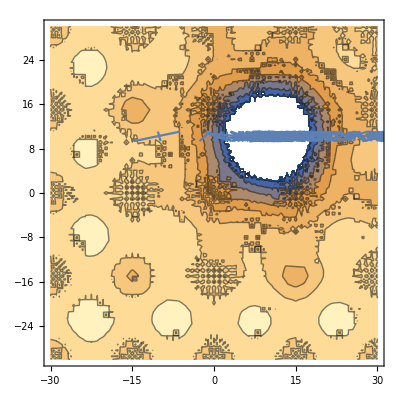

```mathematica
Show[
ContourPlot[ShiftOverBy[{10, 10}, ackleyN]@Table[xx[i], {i, 2}], {xx[1], -30, 30}, {xx[2], -30, 30}],
ListPlot[iterate, Joined-> True]
]
```